# Call Python to compute CY metrics

Getting started
The easiest thing to get started would be to just run the entire notebook.

Documentation
• To see all functions currently available run ?cymetric
• If you want to see detailed documentation for any of the functions (including its input, options, output, examples), run e.g. ?TrainNN. Running Options[TrainNN] gives you a list of the options for this function and their default values. 
• The value of all global options can be checked with GetGlobalOptions[]

Setting up the program
In order to install the program, you just need to call Setup[] (Setup will detect whether you have run it before and not do anything if everything is already setup; so it does not hurt to just compile the entire notebook every time). Setup[] will try to discover python3 on your system and create a virtual environment with all required packages installed. For some combinations of Python and (older versions of) Mathematica, setup will automatically apply a bug fix. The program will create a text file (with the same name as the notebook, with an extension “.m”, at the same location as the notebook file) that stores some options, e.g. the location of the virtual environment to use for future runs.
More advanced (if you do not want to just call Setup[] and be done with it):
1.) If you already have a python environment that you want to use, you need to “pip install --user pyzmq” for it to work with Mathematica.  
2.) Then setup the package to use this python interpreter with ChangeSetting[“Python”,”<path/to/python>”].

## Setup Python for CY metrics

Load the package from the web.
You can also download the package file and copy it to Mathematica’s Application folder. 
To find the folder execute the following command in Mathematica: FileNameJoin[{$UserBaseDirectory,”/Applications”}] 
Then just copy the file https://github.com/pythoncymetric/cymetric/tree/main/cymetric/wolfram/cymetric.m to this directory and load it with  <<cymetric`

```mathematica
Quit[]
```

```mathematica
Get["https://raw.githubusercontent.com/pythoncymetric/cymetric/main/cymetric/wolfram/cymetric.m"];
```

```mathematica
(*Path where the virtual environment for python will be created. Defaults to the User's Home Directory*)
PathToVenv=FileNameJoin[{$HomeDirectory,"venv-mathematica"}];
(*If you already have an environment that you want to use, set the path here*)
(*ChangeSetting["Python","<path/to/python>"]*)
python=Setup[PathToVenv];
```

## Quintic

### Compute Points and Metric

To look at the parameters and options of a function, simply call ?<FunctionName> and Options[<FunctionName>]

```mathematica
?GeneratePoints
Options[GeneratePoints]
```

{KahlerModuli→{},Points→200000}

Now we generate some points. We set the output Directory to “Quintic”

```mathematica
??GeneratePoints
```

```mathematica
outDir=FileNameJoin[{NotebookDirectory[],"Quintic"}];
ChangeSetting["Dir",outDir];
```

```mathematica
poly={Subscript[z, 0]^5+Subscript[z, 1]^5+Subscript[z, 2]^5+Subscript[z, 3]^5+Subscript[z, 4]^5+0 Subscript[z, 0] Subscript[z, 1] Subscript[z, 2] Subscript[z, 3] Subscript[z, 4]};
pdim={4};kmod={1};
```

```mathematica
poly={6 I Subscript[x, 1,0] Subscript[x, 3,0]^2+72 Subscript[x, 1,1] Subscript[x, 3,0]^2+60 Subscript[x, 1,0] Subscript[x, 3,0] Subscript[x, 3,1]+89 Subscript[x, 1,1] Subscript[x, 3,0] Subscript[x, 3,1]+3 Subscript[x, 1,0] Subscript[x, 3,1]^2+90 Subscript[x, 1,1] Subscript[x, 3,1]^2+91 Subscript[x, 1,0] Subscript[x, 3,0] Subscript[x, 3,2]+30 Subscript[x, 1,1] Subscript[x, 3,0] Subscript[x, 3,2]+43 Subscript[x, 1,0] Subscript[x, 3,1] Subscript[x, 3,2]+24 Subscript[x, 1,1] Subscript[x, 3,1] Subscript[x, 3,2]+21 Subscript[x, 1,0] Subscript[x, 3,2]^2+49 Subscript[x, 1,1] Subscript[x, 3,2]^2+68 Subscript[x, 1,0] Subscript[x, 3,0] Subscript[x, 3,3]+28 Subscript[x, 1,1] Subscript[x, 3,0] Subscript[x, 3,3]+42 Subscript[x, 1,0] Subscript[x, 3,1] Subscript[x, 3,3]+36 Subscript[x, 1,1] Subscript[x, 3,1] Subscript[x, 3,3]+37 Subscript[x, 1,0] Subscript[x, 3,2] Subscript[x, 3,3]+25 Subscript[x, 1,1] Subscript[x, 3,2] Subscript[x, 3,3]+55 Subscript[x, 1,0] Subscript[x, 3,3]^2+57 Subscript[x, 1,1] Subscript[x, 3,3]^2+85 Subscript[x, 1,0] Subscript[x, 3,0] Subscript[x, 3,4]+52 Subscript[x, 1,1] Subscript[x, 3,0] Subscript[x, 3,4]+38 Subscript[x, 1,0] Subscript[x, 3,1] Subscript[x, 3,4]+61 Subscript[x, 1,1] Subscript[x, 3,1] Subscript[x, 3,4]+86 Subscript[x, 1,0] Subscript[x, 3,2] Subscript[x, 3,4]+87 Subscript[x, 1,1] Subscript[x, 3,2] Subscript[x, 3,4]+38 Subscript[x, 1,0] Subscript[x, 3,3] Subscript[x, 3,4]+45 Subscript[x, 1,1] Subscript[x, 3,3] Subscript[x, 3,4]+88 Subscript[x, 1,0] Subscript[x, 3,4]^2+11 Subscript[x, 1,1] Subscript[x, 3,4]^2,100 Subscript[x, 1,0] Subscript[x, 3,0]+19 Subscript[x, 1,1] Subscript[x, 3,0]+73 Subscript[x, 1,0] Subscript[x, 3,1]+97 Subscript[x, 1,1] Subscript[x, 3,1]+70 Subscript[x, 1,0] Subscript[x, 3,2]+47 Subscript[x, 1,1] Subscript[x, 3,2]+4 Subscript[x, 1,0] Subscript[x, 3,3]+56 Subscript[x, 1,1] Subscript[x, 3,3]+49 Subscript[x, 1,0] Subscript[x, 3,4]+15 Subscript[x, 1,1] Subscript[x, 3,4],27 Subscript[x, 2,0]^2 Subscript[x, 3,0]^2+100 Subscript[x, 2,0] Subscript[x, 2,1] Subscript[x, 3,0]^2+72 Subscript[x, 2,1]^2 Subscript[x, 3,0]^2+31 Subscript[x, 2,0]^2 Subscript[x, 3,0] Subscript[x, 3,1]+20 Subscript[x, 2,0] Subscript[x, 2,1] Subscript[x, 3,0] Subscript[x, 3,1]+72 Subscript[x, 2,1]^2 Subscript[x, 3,0] Subscript[x, 3,1]+54 Subscript[x, 2,0]^2 Subscript[x, 3,1]^2+50 Subscript[x, 2,0] Subscript[x, 2,1] Subscript[x, 3,1]^2+84 Subscript[x, 2,1]^2 Subscript[x, 3,1]^2+40 Subscript[x, 2,0]^2 Subscript[x, 3,0] Subscript[x, 3,2]+73 Subscript[x, 2,0] Subscript[x, 2,1] Subscript[x, 3,0] Subscript[x, 3,2]+Subscript[x, 2,1]^2 Subscript[x, 3,0] Subscript[x, 3,2]+24 Subscript[x, 2,0]^2 Subscript[x, 3,1] Subscript[x, 3,2]+40 Subscript[x, 2,0] Subscript[x, 2,1] Subscript[x, 3,1] Subscript[x, 3,2]+99 Subscript[x, 2,1]^2 Subscript[x, 3,1] Subscript[x, 3,2]+86 Subscript[x, 2,0]^2 Subscript[x, 3,2]^2+97 Subscript[x, 2,0] Subscript[x, 2,1] Subscript[x, 3,2]^2+89 Subscript[x, 2,1]^2 Subscript[x, 3,2]^2+42 Subscript[x, 2,0]^2 Subscript[x, 3,0] Subscript[x, 3,3]+85 Subscript[x, 2,0] Subscript[x, 2,1] Subscript[x, 3,0] Subscript[x, 3,3]+41 Subscript[x, 2,1]^2 Subscript[x, 3,0] Subscript[x, 3,3]+33 Subscript[x, 2,0]^2 Subscript[x, 3,1] Subscript[x, 3,3]+19 Subscript[x, 2,0] Subscript[x, 2,1] Subscript[x, 3,1] Subscript[x, 3,3]+70 Subscript[x, 2,1]^2 Subscript[x, 3,1] Subscript[x, 3,3]+40 Subscript[x, 2,0]^2 Subscript[x, 3,2] Subscript[x, 3,3]+17 Subscript[x, 2,0] Subscript[x, 2,1] Subscript[x, 3,2] Subscript[x, 3,3]+90 Subscript[x, 2,1]^2 Subscript[x, 3,2] Subscript[x, 3,3]+73 Subscript[x, 2,0]^2 Subscript[x, 3,3]^2+76 Subscript[x, 2,0] Subscript[x, 2,1] Subscript[x, 3,3]^2+40 Subscript[x, 2,1]^2 Subscript[x, 3,3]^2+69 Subscript[x, 2,0]^2 Subscript[x, 3,0] Subscript[x, 3,4]+39 Subscript[x, 2,0] Subscript[x, 2,1] Subscript[x, 3,0] Subscript[x, 3,4]+44 Subscript[x, 2,1]^2 Subscript[x, 3,0] Subscript[x, 3,4]+56 Subscript[x, 2,0]^2 Subscript[x, 3,1] Subscript[x, 3,4]+35 Subscript[x, 2,0] Subscript[x, 2,1] Subscript[x, 3,1] Subscript[x, 3,4]+74 Subscript[x, 2,1]^2 Subscript[x, 3,1] Subscript[x, 3,4]+52 Subscript[x, 2,0]^2 Subscript[x, 3,2] Subscript[x, 3,4]+80 Subscript[x, 2,0] Subscript[x, 2,1] Subscript[x, 3,2] Subscript[x, 3,4]+38 Subscript[x, 2,1]^2 Subscript[x, 3,2] Subscript[x, 3,4]+88 Subscript[x, 2,0]^2 Subscript[x, 3,3] Subscript[x, 3,4]+56 Subscript[x, 2,0] Subscript[x, 2,1] Subscript[x, 3,3] Subscript[x, 3,4]+8 Subscript[x, 2,1]^2 Subscript[x, 3,3] Subscript[x, 3,4]+71 Subscript[x, 2,0]^2 Subscript[x, 3,4]^2+63 Subscript[x, 2,0] Subscript[x, 2,1] Subscript[x, 3,4]^2+56 Subscript[x, 2,1]^2 Subscript[x, 3,4]^2};
pdim={1,1,4};kmod={1,1,1};
```

```mathematica
res=GeneratePoints[poly,pdim,"Points"->100000,"KahlerModuli"->kmod];
```

Warning: No variables specified, assuming alphabetical monomial ordering.

Generating 100000 points...

Configuration matrix: {{5}}

Number of Parameters per P^n: {1}

Number of points on CY from one ambient space intersection: 5

Now generating 100000 points...

done.

Writing points to /Users/ruehle/GitHub/cymetric/notebooks/Quintic/points.pickle

/Users/ruehle/venv-mathematica/lib/python3.9/site-packages/numpy/linalg/linalg.py:2139: RuntimeWarning: divide by zero encountered in det

r = _umath_linalg.det(a, signature=signature)

/Users/ruehle/venv-mathematica/lib/python3.9/site-packages/numpy/linalg/linalg.py:2139: RuntimeWarning: invalid value encountered in det

r = _umath_linalg.det(a, signature=signature)

Now we train the NN. We choose the PhiFS model here. (Training can be made faster if one sets “EvaluateModel”->False). 
We also set Verbose to 3 to see some more info during the training process.

```mathematica
history=TrainNN["Epochs"->30,"EvaluateModel"->True,"Verbose"->3];
```

DEBUG:mathematica:{'ActivationFunctions': array(['gelu', 'gelu', 'gelu'], dtype='<U4'), 'Alphas': array([1., 1., 1., 1., 1.]), 'BatchSizes': array([   64, 50000]), 'Dir': '/Users/ruehle/GitHub/cymetric/notebooks/Quintic', 'DisableGPU': False, 'HiddenLayers': array([64, 64, 64]), 'LearningRate': 0.001, 'Model': 'PhiFS', 'Precision': 10, 'PrintLosses': array([ True,  True,  True,  True,  True]), 'PrintMeasures': array([ True,  True,  True,  True,  True]), 'Python': '/Users/ruehle/venv-mathematica/bin/python', 'Verbose': 3, 'Epochs': 30, 'EvaluateModel': True, 'logger_level': 10}

DEBUG:mathematica:Using CPU for computation.

DEBUG:mathematica:Using model PhiFS

WARNING:absl:At this time, the v2.11+ optimizer `tf.keras.optimizers.Adam` runs slowly on M1/M2 Macs, please use the legacy Keras optimizer instead, located at `tf.keras.optimizers.legacy.Adam`.

DEBUG:mathematica:Model: "sequential"

DEBUG:mathematica:_________________________________________________________________

DEBUG:mathematica: Layer (type)                Output Shape              Param #

DEBUG:mathematica:=================================================================

DEBUG:mathematica: dense (Dense)               (None, 64)                704

DEBUG:mathematica:

DEBUG:mathematica: dense_1 (Dense)             (None, 64)                4160

DEBUG:mathematica:

DEBUG:mathematica: dense_2 (Dense)             (None, 64)                4160

DEBUG:mathematica:

DEBUG:mathematica: dense_3 (Dense)             (None, 1)                 64

DEBUG:mathematica:

DEBUG:mathematica:=================================================================

DEBUG:mathematica:Total params: 9088 (35.50 KB)

DEBUG:mathematica:Trainable params: 9088 (35.50 KB)

DEBUG:mathematica:Non-trainable params: 0 (0.00 Byte)

DEBUG:mathematica:_________________________________________________________________

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch  1/30

1407/1407 - 11s - sigma_loss: 0.2234 - transition_loss: 0.0069 - volk_loss: 0.0000e+00 - 11s/epoch - 8ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.1616

- Transition measure val: 0.0046

- Ricci measure val:      1.3290

- Volk val:               6.2288

2/2 - 18s - sigma_loss: 0.2423 - transition_loss: 0.0000e+00 - volk_loss: 0.4616 - sigma_val: 0.1616 - transition_val: 0.0046 - ricci_val: 1.3290 - volk_val: 6.2288 - 18s/epoch - 9s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch  2/30

1407/1407 - 13s - sigma_loss: 0.1511 - transition_loss: 0.0023 - volk_loss: 0.0000e+00 - 13s/epoch - 9ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.1576

- Transition measure val: 0.0030

- Ricci measure val:      1.1873

- Volk val:               5.8998

2/2 - 9s - sigma_loss: 0.2146 - transition_loss: 0.0000e+00 - volk_loss: 0.3448 - sigma_val: 0.1576 - transition_val: 0.0030 - ricci_val: 1.1873 - volk_val: 5.8998 - 9s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch  3/30

1407/1407 - 12s - sigma_loss: 0.1470 - transition_loss: 0.0019 - volk_loss: 0.0000e+00 - 12s/epoch - 8ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.1520

- Transition measure val: 0.0041

- Ricci measure val:      1.2460

- Volk val:               5.8691

2/2 - 9s - sigma_loss: 0.2034 - transition_loss: 0.0000e+00 - volk_loss: 0.2798 - sigma_val: 0.1520 - transition_val: 0.0041 - ricci_val: 1.2460 - volk_val: 5.8691 - 9s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch  4/30

1407/1407 - 12s - sigma_loss: 0.1422 - transition_loss: 0.0018 - volk_loss: 0.0000e+00 - 12s/epoch - 9ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.1457

- Transition measure val: 0.0024

- Ricci measure val:      1.1798

- Volk val:               5.5588

2/2 - 9s - sigma_loss: 0.1681 - transition_loss: 0.0000e+00 - volk_loss: 0.2573 - sigma_val: 0.1457 - transition_val: 0.0024 - ricci_val: 1.1798 - volk_val: 5.5588 - 9s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch  5/30

1407/1407 - 11s - sigma_loss: 0.1362 - transition_loss: 0.0019 - volk_loss: 0.0000e+00 - 11s/epoch - 8ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.1368

- Transition measure val: 0.0031

- Ricci measure val:      1.0000

- Volk val:               5.6242

2/2 - 9s - sigma_loss: 0.1651 - transition_loss: 0.0000e+00 - volk_loss: 0.2509 - sigma_val: 0.1368 - transition_val: 0.0031 - ricci_val: 1.0000 - volk_val: 5.6242 - 9s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch  6/30

1407/1407 - 12s - sigma_loss: 0.1204 - transition_loss: 0.0022 - volk_loss: 0.0000e+00 - 12s/epoch - 8ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.1124

- Transition measure val: 0.0027

- Ricci measure val:      0.6535

- Volk val:               5.4819

2/2 - 10s - sigma_loss: 0.1323 - transition_loss: 0.0000e+00 - volk_loss: 0.2349 - sigma_val: 0.1124 - transition_val: 0.0027 - ricci_val: 0.6535 - volk_val: 5.4819 - 10s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch  7/30

1407/1407 - 12s - sigma_loss: 0.0915 - transition_loss: 0.0029 - volk_loss: 0.0000e+00 - 12s/epoch - 8ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0800

- Transition measure val: 0.0031

- Ricci measure val:      0.4003

- Volk val:               5.6479

2/2 - 10s - sigma_loss: 0.1148 - transition_loss: 0.0000e+00 - volk_loss: 0.2360 - sigma_val: 0.0800 - transition_val: 0.0031 - ricci_val: 0.4003 - volk_val: 5.6479 - 10s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch  8/30

1407/1407 - 12s - sigma_loss: 0.0714 - transition_loss: 0.0026 - volk_loss: 0.0000e+00 - 12s/epoch - 8ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0702

- Transition measure val: 0.0024

- Ricci measure val:      0.2767

- Volk val:               4.5491

2/2 - 10s - sigma_loss: 0.0975 - transition_loss: 0.0000e+00 - volk_loss: 0.2108 - sigma_val: 0.0702 - transition_val: 0.0024 - ricci_val: 0.2767 - volk_val: 4.5491 - 10s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch  9/30

1407/1407 - 12s - sigma_loss: 0.0610 - transition_loss: 0.0021 - volk_loss: 0.0000e+00 - 12s/epoch - 8ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0560

- Transition measure val: 0.0019

- Ricci measure val:      0.2270

- Volk val:               4.5293

2/2 - 10s - sigma_loss: 0.0828 - transition_loss: 0.0000e+00 - volk_loss: 0.1699 - sigma_val: 0.0560 - transition_val: 0.0019 - ricci_val: 0.2270 - volk_val: 4.5293 - 10s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch 10/30

1407/1407 - 11s - sigma_loss: 0.0538 - transition_loss: 0.0017 - volk_loss: 0.0000e+00 - 11s/epoch - 8ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0501

- Transition measure val: 0.0015

- Ricci measure val:      0.2041

- Volk val:               4.6637

2/2 - 10s - sigma_loss: 0.0743 - transition_loss: 0.0000e+00 - volk_loss: 0.1565 - sigma_val: 0.0501 - transition_val: 0.0015 - ricci_val: 0.2041 - volk_val: 4.6637 - 10s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch 11/30

1407/1407 - 13s - sigma_loss: 0.0470 - transition_loss: 0.0014 - volk_loss: 0.0000e+00 - 13s/epoch - 9ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0434

- Transition measure val: 0.0014

- Ricci measure val:      0.1685

- Volk val:               4.6720

2/2 - 9s - sigma_loss: 0.0662 - transition_loss: 0.0000e+00 - volk_loss: 0.1318 - sigma_val: 0.0434 - transition_val: 0.0014 - ricci_val: 0.1685 - volk_val: 4.6720 - 9s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch 12/30

1407/1407 - 13s - sigma_loss: 0.0405 - transition_loss: 0.0011 - volk_loss: 0.0000e+00 - 13s/epoch - 9ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0342

- Transition measure val: 0.0011

- Ricci measure val:      0.1416

- Volk val:               4.7451

2/2 - 10s - sigma_loss: 0.0536 - transition_loss: 0.0000e+00 - volk_loss: 0.1323 - sigma_val: 0.0342 - transition_val: 0.0011 - ricci_val: 0.1416 - volk_val: 4.7451 - 10s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch 13/30

1407/1407 - 14s - sigma_loss: 0.0359 - transition_loss: 9.4415e-04 - volk_loss: 0.0000e+00 - 14s/epoch - 10ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0299

- Transition measure val: 9.5794e-04

- Ricci measure val:      0.1409

- Volk val:               5.2781

2/2 - 10s - sigma_loss: 0.0474 - transition_loss: 0.0000e+00 - volk_loss: 0.1044 - sigma_val: 0.0299 - transition_val: 9.5794e-04 - ricci_val: 0.1409 - volk_val: 5.2781 - 10s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch 14/30

1407/1407 - 14s - sigma_loss: 0.0323 - transition_loss: 8.1923e-04 - volk_loss: 0.0000e+00 - 14s/epoch - 10ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0287

- Transition measure val: 8.9599e-04

- Ricci measure val:      0.1181

- Volk val:               4.7338

2/2 - 10s - sigma_loss: 0.0498 - transition_loss: 0.0000e+00 - volk_loss: 0.1084 - sigma_val: 0.0287 - transition_val: 8.9599e-04 - ricci_val: 0.1181 - volk_val: 4.7338 - 10s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch 15/30

1407/1407 - 13s - sigma_loss: 0.0299 - transition_loss: 7.2066e-04 - volk_loss: 0.0000e+00 - 13s/epoch - 9ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0268

- Transition measure val: 7.1919e-04

- Ricci measure val:      0.1291

- Volk val:               5.2538

2/2 - 11s - sigma_loss: 0.0419 - transition_loss: 0.0000e+00 - volk_loss: 0.0890 - sigma_val: 0.0268 - transition_val: 7.1919e-04 - ricci_val: 0.1291 - volk_val: 5.2538 - 11s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch 16/30

1407/1407 - 13s - sigma_loss: 0.0282 - transition_loss: 6.5575e-04 - volk_loss: 0.0000e+00 - 13s/epoch - 9ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0249

- Transition measure val: 6.4765e-04

- Ricci measure val:      0.1225

- Volk val:               5.2456

2/2 - 10s - sigma_loss: 0.0401 - transition_loss: 0.0000e+00 - volk_loss: 0.0890 - sigma_val: 0.0249 - transition_val: 6.4765e-04 - ricci_val: 0.1225 - volk_val: 5.2456 - 10s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch 17/30

1407/1407 - 13s - sigma_loss: 0.0266 - transition_loss: 5.9768e-04 - volk_loss: 0.0000e+00 - 13s/epoch - 9ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0232

- Transition measure val: 7.3000e-04

- Ricci measure val:      0.1081

- Volk val:               4.7878

2/2 - 10s - sigma_loss: 0.0424 - transition_loss: 0.0000e+00 - volk_loss: 0.0873 - sigma_val: 0.0232 - transition_val: 7.3000e-04 - ricci_val: 0.1081 - volk_val: 4.7878 - 10s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch 18/30

1407/1407 - 13s - sigma_loss: 0.0251 - transition_loss: 5.5151e-04 - volk_loss: 0.0000e+00 - 13s/epoch - 9ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0214

- Transition measure val: 5.9501e-04

- Ricci measure val:      0.1073

- Volk val:               4.8658

2/2 - 10s - sigma_loss: 0.0343 - transition_loss: 0.0000e+00 - volk_loss: 0.0919 - sigma_val: 0.0214 - transition_val: 5.9501e-04 - ricci_val: 0.1073 - volk_val: 4.8658 - 10s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch 19/30

1407/1407 - 12s - sigma_loss: 0.0239 - transition_loss: 5.1171e-04 - volk_loss: 0.0000e+00 - 12s/epoch - 9ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0204

- Transition measure val: 6.3229e-04

- Ricci measure val:      0.1042

- Volk val:               4.7954

2/2 - 11s - sigma_loss: 0.0380 - transition_loss: 0.0000e+00 - volk_loss: 0.0724 - sigma_val: 0.0204 - transition_val: 6.3229e-04 - ricci_val: 0.1042 - volk_val: 4.7954 - 11s/epoch - 6s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch 20/30

1407/1407 - 12s - sigma_loss: 0.0229 - transition_loss: 4.8770e-04 - volk_loss: 0.0000e+00 - 12s/epoch - 9ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0191

- Transition measure val: 5.7139e-04

- Ricci measure val:      0.1033

- Volk val:               4.8334

2/2 - 9s - sigma_loss: 0.0337 - transition_loss: 0.0000e+00 - volk_loss: 0.0714 - sigma_val: 0.0191 - transition_val: 5.7139e-04 - ricci_val: 0.1033 - volk_val: 4.8334 - 9s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch 21/30

1407/1407 - 12s - sigma_loss: 0.0218 - transition_loss: 4.5554e-04 - volk_loss: 0.0000e+00 - 12s/epoch - 8ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0184

- Transition measure val: 5.6074e-04

- Ricci measure val:      0.1010

- Volk val:               4.8536

2/2 - 10s - sigma_loss: 0.0328 - transition_loss: 0.0000e+00 - volk_loss: 0.0780 - sigma_val: 0.0184 - transition_val: 5.6074e-04 - ricci_val: 0.1010 - volk_val: 4.8536 - 10s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch 22/30

1407/1407 - 12s - sigma_loss: 0.0208 - transition_loss: 4.3348e-04 - volk_loss: 0.0000e+00 - 12s/epoch - 8ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0179

- Transition measure val: 5.0027e-04

- Ricci measure val:      0.0976

- Volk val:               4.8587

2/2 - 10s - sigma_loss: 0.0323 - transition_loss: 0.0000e+00 - volk_loss: 0.0746 - sigma_val: 0.0179 - transition_val: 5.0027e-04 - ricci_val: 0.0976 - volk_val: 4.8587 - 10s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch 23/30

1407/1407 - 12s - sigma_loss: 0.0205 - transition_loss: 4.0687e-04 - volk_loss: 0.0000e+00 - 12s/epoch - 9ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0184

- Transition measure val: 5.5654e-04

- Ricci measure val:      0.0964

- Volk val:               4.8358

2/2 - 10s - sigma_loss: 0.0336 - transition_loss: 0.0000e+00 - volk_loss: 0.0690 - sigma_val: 0.0184 - transition_val: 5.5654e-04 - ricci_val: 0.0964 - volk_val: 4.8358 - 10s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch 24/30

1407/1407 - 12s - sigma_loss: 0.0192 - transition_loss: 3.8305e-04 - volk_loss: 0.0000e+00 - 12s/epoch - 9ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0159

- Transition measure val: 4.8883e-04

- Ricci measure val:      0.0906

- Volk val:               4.8620

2/2 - 11s - sigma_loss: 0.0293 - transition_loss: 0.0000e+00 - volk_loss: 0.0593 - sigma_val: 0.0159 - transition_val: 4.8883e-04 - ricci_val: 0.0906 - volk_val: 4.8620 - 11s/epoch - 6s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch 25/30

1407/1407 - 12s - sigma_loss: 0.0186 - transition_loss: 3.6408e-04 - volk_loss: 0.0000e+00 - 12s/epoch - 9ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0151

- Transition measure val: 4.6025e-04

- Ricci measure val:      0.0891

- Volk val:               4.8663

2/2 - 10s - sigma_loss: 0.0286 - transition_loss: 0.0000e+00 - volk_loss: 0.0563 - sigma_val: 0.0151 - transition_val: 4.6025e-04 - ricci_val: 0.0891 - volk_val: 4.8663 - 10s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch 26/30

1407/1407 - 12s - sigma_loss: 0.0182 - transition_loss: 3.4651e-04 - volk_loss: 0.0000e+00 - 12s/epoch - 8ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0144

- Transition measure val: 3.9977e-04

- Ricci measure val:      0.0909

- Volk val:               5.1909

2/2 - 9s - sigma_loss: 0.0269 - transition_loss: 0.0000e+00 - volk_loss: 0.0603 - sigma_val: 0.0144 - transition_val: 3.9977e-04 - ricci_val: 0.0909 - volk_val: 5.1909 - 9s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch 27/30

1407/1407 - 12s - sigma_loss: 0.0173 - transition_loss: 3.3376e-04 - volk_loss: 0.0000e+00 - 12s/epoch - 9ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0153

- Transition measure val: 3.3889e-04

- Ricci measure val:      0.0886

- Volk val:               5.1916

2/2 - 10s - sigma_loss: 0.0274 - transition_loss: 0.0000e+00 - volk_loss: 0.0636 - sigma_val: 0.0153 - transition_val: 3.3889e-04 - ricci_val: 0.0886 - volk_val: 5.1916 - 10s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch 28/30

1407/1407 - 12s - sigma_loss: 0.0169 - transition_loss: 3.1874e-04 - volk_loss: 0.0000e+00 - 12s/epoch - 9ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0151

- Transition measure val: 4.3423e-04

- Ricci measure val:      0.0792

- Volk val:               4.8603

2/2 - 10s - sigma_loss: 0.0280 - transition_loss: 0.0000e+00 - volk_loss: 0.0642 - sigma_val: 0.0151 - transition_val: 4.3423e-04 - ricci_val: 0.0792 - volk_val: 4.8603 - 10s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch 29/30

1407/1407 - 13s - sigma_loss: 0.0165 - transition_loss: 3.0858e-04 - volk_loss: 0.0000e+00 - 13s/epoch - 9ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0138

- Transition measure val: 4.4922e-04

- Ricci measure val:      0.0757

- Volk val:               4.8978

2/2 - 10s - sigma_loss: 0.0244 - transition_loss: 0.0000e+00 - volk_loss: 0.0662 - sigma_val: 0.0138 - transition_val: 4.4922e-04 - ricci_val: 0.0757 - volk_val: 4.8978 - 10s/epoch - 5s/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

Epoch 30/30

1407/1407 - 14s - sigma_loss: 0.0161 - transition_loss: 3.0139e-04 - volk_loss: 0.0000e+00 - 14s/epoch - 10ms/step

WARNING:absl:There is a known slowdown when using v2.11+ Keras optimizers on M1/M2 Macs. Falling back to the legacy Keras optimizer, i.e., `tf.keras.optimizers.legacy.Adam`.

- Sigma measure val:      0.0126

- Transition measure val: 4.2279e-04

- Ricci measure val:      0.0716

- Volk val:               4.9172

2/2 - 10s - sigma_loss: 0.0233 - transition_loss: 0.0000e+00 - volk_loss: 0.0597 - sigma_val: 0.0126 - transition_val: 4.2279e-04 - ricci_val: 0.0716 - volk_val: 4.9172 - 10s/epoch - 5s/step

Writing training information to /Users/ruehle/GitHub/cymetric/notebooks/Quintic/training_history_mathematica.m

```mathematica
history
```

<|volk_loss→{0.461643,0.344795,0.279798,0.257303,0.250915,0.234875,0.235997,0.210833,0.169878,0.156503,0.131757,0.132266,0.104398,0.108419,0.0889822,0.0889635,0.08734,0.0918741,0.0723893,0.0713864,0.0780032,0.0746023,0.0690173,0.059297,0.0562714,0.0603293,0.0636302,0.0642129,0.066161,0.0596793},volk_val→{6.22881,5.89984,5.86909,5.55885,5.6242,5.48187,5.64791,4.54914,4.52932,4.66375,4.67198,4.74512,5.2781,4.73383,5.25376,5.2456,4.78776,4.86583,4.79537,4.83341,4.85357,4.85867,4.8358,4.86199,4.86627,5.19091,5.19155,4.86025,4.89777,4.91721},sigma_val→{0.161645,0.157612,0.152017,0.145746,0.136829,0.112426,0.0799827,0.0701985,0.0560385,0.0500611,0.0434165,0.0342445,0.0299461,0.0287172,0.0267551,0.0248981,0.0231861,0.0213972,0.0203831,0.0191464,0.0183821,0.0178763,0.018432,0.0159149,0.0151189,0.0143983,0.0152693,0.0151281,0.0137857,0.012571},sigma_loss→{0.242326,0.214613,0.203403,0.168081,0.165079,0.132252,0.114802,0.0975053,0.0828373,0.0743071,0.0661582,0.0535879,0.0473676,0.0497813,0.0419383,0.0401312,0.0423674,0.0342782,0.0380378,0.03369,0.0327613,0.0322733,0.0335789,0.0292515,0.0285913,0.0269346,0.0273831,0.0279561,0.0243942,0.0232945},transition_loss→{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},transition_val→{0.00458299,0.00301731,0.00412112,0.00243772,0.00312748,0.00269981,0.00306017,0.0023798,0.00193053,0.00151697,0.0013519,0.00113201,0.000957938,0.000895985,0.000719193,0.000647653,0.000730001,0.00059501,0.000632288,0.00057139,0.000560738,0.000500271,0.000556537,0.000488825,0.000460251,0.000399773,0.000338885,0.000434233,0.000449222,0.000422785},ricci_val→{1.32896,1.18734,1.24596,1.17978,1.00003,0.653516,0.400348,0.27669,0.22704,0.204103,0.168459,0.141565,0.140903,0.118083,0.129056,0.122531,0.108121,0.107331,0.104233,0.103284,0.100998,0.0976115,0.0963534,0.090637,0.0891078,0.0908963,0.0886202,0.079238,0.0757006,0.0715955},epochs→{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}|>

We can access the generated points easily

```mathematica
pts=GetPoints["all"];
pts[[1]]
```

{0.912776+0.319828 ⅈ,0.570179+0.733172 ⅈ,1.,-0.403531+0.075955 ⅈ,0.14365-0.163143 ⅈ}

We can access the weights of the points with respect to the auxiliary measure and the trained CY metric. 
The distribution should become peaked for the CY metric around a single value, since J^3 and Ω^2 are proportional.

```mathematica
weights=GetWeights["all"];
weightsCY=GetCYWeights["all"];
```

/Users/ruehle/venv-mathematica/lib/python3.9/site-packages/numpy/linalg/linalg.py:2139: RuntimeWarning: divide by zero encountered in det

r = _umath_linalg.det(a, signature=signature)

/Users/ruehle/venv-mathematica/lib/python3.9/site-packages/numpy/linalg/linalg.py:2139: RuntimeWarning: invalid value encountered in det

r = _umath_linalg.det(a, signature=signature)

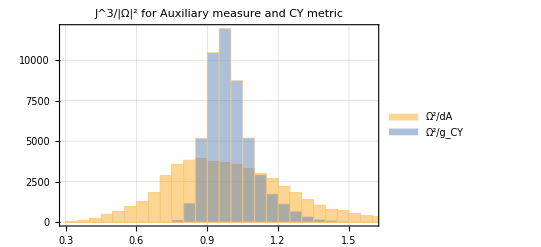

```mathematica
Histogram[{weights/Mean[weights],weightsCY/Mean[weightsCY]},PlotLabel->"J^3/|Ω|^2 for Auxiliary measure and CY metric",PlotTheme->"Detailed",ChartLegends->{ "Ω^2/dA","Ω^2/g_CY"}]
```

To actually access the CY metric, we just call CYMetric on some points

```mathematica
metrics=CYMetric[{{1,2,3,4,5}}];
(*NOTE: The code does not check whether the point is actually on the CY*)
```

```mathematica
metrics=CYMetric[pts];
```

```mathematica
metrics[[1]]//Chop//MatrixForm
```

(0.117129-1.28057×10^-9 ⅈ | 0.0028318+0.00793517 ⅈ | 0.0105414+0.0223561 ⅈ
0.0028318-0.00793517 ⅈ | 0.103159+9.8953×10^-10 ⅈ | -0.0136983-0.0139534 ⅈ
0.0105414-0.0223561 ⅈ | -0.0136983+0.0139534 ⅈ | 0.112784+2.32831×10^-10 ⅈ)

And the volume can be computed by integrating det(g). We compare the Kahler classes of the Fubini-Study and the CY metric, and also look at the actual value as computed from ∫J^3

```mathematica
auxWeights=GetAuxiliaryWeights["all"];
gFSs=FSMetric[pts,{1}];
gCYs=CYMetric[pts];
volFS=Round[Mean[Re[auxWeights (Det/@gFSs)]],0.1];
volCY=Round[Mean[Re[auxWeights (Det/@gCYs)]],0.1];
volInt=5;
Print["Kahler moduli:  ",{1}];
Print["Actual volume:  ",volInt];
Print["FS volume:      ",volFS];
Print["CY volume:      ",volCY];
```

Kahler moduli:  {1}

Actual volume:  5

FS volume:      5.

CY volume:      5.

For the Phi Model, we can also get the Kahler potential

```mathematica
kahler=GetKahlerPotential[pts];
kahler[[;;10]]
```

{0.328003,0.294206,0.341697,0.350628,0.2517,0.257643,0.293327,0.251553,0.285843,0.287078}

### Plot losses

```mathematica
history
```

<|sigma_loss→{0.161506,0.127558,0.100382,0.0844527,0.0786316,0.0753507,0.0719662,0.0701932,0.069417,0.0683528,0.0676854,0.0672523,0.0666325,0.0662399,0.0656526,0.0653093,0.0649564,0.0642834,0.0634489,0.0625384,0.0612094,0.0601294,0.0587451,0.0575448,0.0561747,0.0545453,0.0528727,0.0510253,0.0490354,0.0474367,0.0460083,0.0446611,0.0434437,0.0422694,0.0412269,0.0401281,0.039416,0.0385465,0.0377433,0.0372101,0.0364471,0.0358251,0.0350636,0.034366,0.0335409,0.0327322,0.0318112,0.0311377,0.0303789,0.0297212},kaehler_loss→{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},transition_loss→{0.00555381,0.00236893,0.00252454,0.0021886,0.00178435,0.00151204,0.00124271,0.00103625,0.000924976,0.000808117,0.000729431,0.000669969,0.000632045,0.00057992,0.000539704,0.000523443,0.000508176,0.000495878,0.000508004,0.000508919,0.00053051,0.000547115,0.000538084,0.000561713,0.000568579,0.000605532,0.000620716,0.000656036,0.000669734,0.000670843,0.000652542,0.000640534,0.0006185,0.00060136,0.000571825,0.00055361,0.00053817,0.000515424,0.000489965,0.000474854,0.000462195,0.000435924,0.000427323,0.000410194,0.000392626,0.000373084,0.000353113,0.000329879,0.000316104,0.000306365},ricci_loss→{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},sigma_val→{0.13317,0.111256,0.0976588,0.0872256,0.0820675,0.0800537,0.0762164,0.0771138,0.0760514,0.0751125,0.0747849,0.0743746,0.0740444,0.0754804,0.074633,0.0738001,0.0728842,0.0724806,0.0709871,0.0718881,0.0690101,0.0680953,0.0667803,0.0641863,0.0625917,0.0606075,0.0569503,0.0562965,0.0533878,0.0528378,0.0508666,0.0472707,0.0471389,0.0456457,0.0440276,0.0442379,0.0444127,0.0427669,0.041171,0.0401935,0.0384806,0.0390362,0.0381209,0.0366997,0.0362191,0.0346474,0.034176,0.0332592,0.032856,0.0316171},kaehler_val→{5.56285×10^-15,5.87313×10^-15,6.39338×10^-15,6.34354×10^-15,6.29746×10^-15,6.04402×10^-15,6.16258×10^-15,6.09701×10^-15,5.97775×10^-15,6.04263×10^-15,6.00461×10^-15,6.01438×10^-15,6.0711×10^-15,6.04418×10^-15,5.89882×10^-15,5.87945×10^-15,6.05954×10^-15,5.96545×10^-15,5.95886×10^-15,5.98356×10^-15,5.98613×10^-15,5.98745×10^-15,6.06606×10^-15,6.00846×10^-15,6.13574×10^-15,6.09739×10^-15,6.08859×10^-15,6.24304×10^-15,6.22341×10^-15,6.37906×10^-15,6.42602×10^-15,6.33784×10^-15,6.60269×10^-15,6.51439×10^-15,6.53164×10^-15,6.47985×10^-15,6.32818×10^-15,6.52556×10^-15,6.54511×10^-15,6.55517×10^-15,6.55048×10^-15,6.53385×10^-15,6.44489×10^-15,6.51882×10^-15,6.46422×10^-15,6.53671×10^-15,6.44101×10^-15,6.39969×10^-15,6.41247×10^-15,6.33059×10^-15},transition_val→{0.00312154,0.00216937,0.0025323,0.00183202,0.00153725,0.00151107,0.00107075,0.000945184,0.000828253,0.000743432,0.000640006,0.000625987,0.000594145,0.000509967,0.000475504,0.000499641,0.000523805,0.000516586,0.00053548,0.000644208,0.000522523,0.000569692,0.000560272,0.000536731,0.000554131,0.000604576,0.000632852,0.000675914,0.000652395,0.00064281,0.000634937,0.000618697,0.000608217,0.000596024,0.00054223,0.000517931,0.000527835,0.000476388,0.000468104,0.000464004,0.000440865,0.00042164,0.000436682,0.000429602,0.000379256,0.000412075,0.000370079,0.000353476,0.000323404,0.000297301},ricci_val→{1.11326,0.612845,0.635567,0.56971,0.581499,0.578902,0.549973,0.549657,0.516449,0.505955,0.5098,0.524115,0.498166,0.489744,0.485337,0.485869,0.508259,0.495798,0.479575,0.476229,0.472101,0.469756,0.463574,0.460965,0.450501,0.455439,0.445281,0.45088,0.444093,0.451888,0.432239,0.43846,0.451041,0.446845,0.434139,0.431565,0.418975,0.418248,0.411258,0.428185,0.414037,0.40383,0.399939,0.401321,0.400435,0.38309,0.378111,0.384314,0.380201,0.381559},volk_val→{5.25534,5.10056,4.91081,5.01047,5.06453,4.75847,5.08494,4.86422,4.99503,4.98604,4.91188,4.94562,4.86999,4.94758,4.90632,4.83609,4.95417,4.8137,4.87383,4.858,4.92131,4.96365,4.93772,4.93533,4.97566,4.96762,4.98091,4.96851,4.90395,4.96186,4.94278,4.97623,4.94363,4.98072,4.93838,4.96218,4.91351,4.98634,4.98174,4.98542,4.98065,4.97262,4.94828,4.98659,5.00549,4.97665,5.01,4.99856,4.97924,5.01413}|>

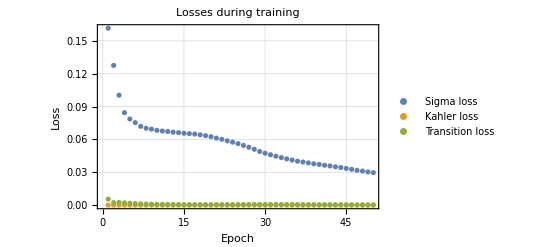

```mathematica
ListPlot[{history[["sigma_loss"]],history[["kaehler_loss"]],history[["transition_loss"]]},PlotLabel->"Losses during training",FrameLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Kahler loss","Transition loss"},PlotTheme->"Detailed"]
```

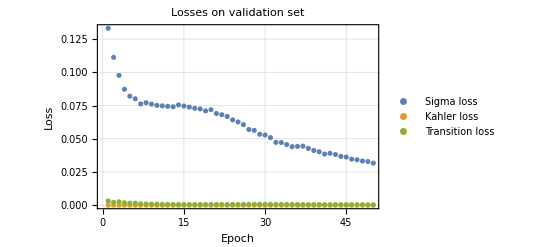

```mathematica
ListPlot[{history[["sigma_val"]],history[["kaehler_val"]],history[["transition_val"]]},PlotLabel->"Losses on validation set",FrameLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Kahler loss","Transition loss"},PlotTheme->"Detailed"]
```

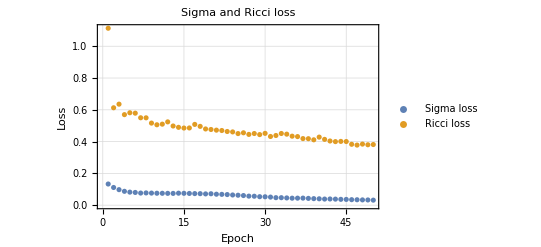

```mathematica
ListPlot[{history[["sigma_val"]],history[["ricci_val"]]},PlotLabel->"Sigma and Ricci loss",FrameLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Ricci loss"},PlotTheme->"Detailed"]
```

```mathematica
SigmaVsRicci=Table[{history[["sigma_val"]][[i]],history[["ricci_val"]][[i]]},{i,Length[history[["sigma_val"]]]}];
```

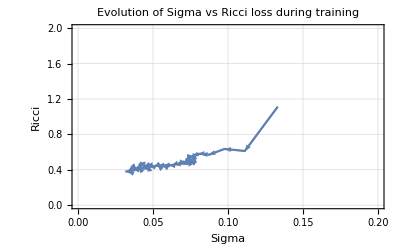

```mathematica
Show@@Join[{ListLinePlot[SigmaVsRicci,PlotLabel->"Evolution of Sigma vs Ricci loss during training",FrameLabel->{"Sigma","Ricci"},PlotRange->{{0,0.2},{0,2}},PlotTheme->"Detailed"]},Table[ListLinePlot[SigmaVsRicci[[i;;i+1]],PlotStyle->Directive[Thick,Arrowheads[.035]]]/.Line->Arrow,{i,Length[SigmaVsRicci]-1}]]
```

### Look at eigenvalues of the metric

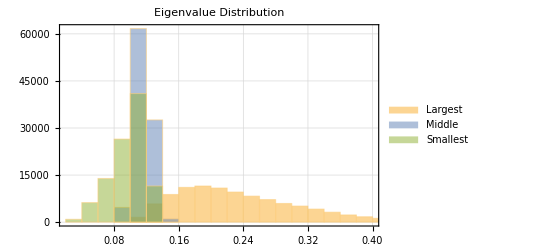

```mathematica
EigVals=Table[Eigenvalues[metrics[[i]]]//Re//Chop,{i,Length[metrics]}];
Histogram[{EigVals[[;;,1]],EigVals[[;;,2]],EigVals[[;;,3]]},PlotLabel->"Eigenvalue Distribution",PlotTheme->"Detailed",ChartLegends->{"Largest", "Middle","Smallest"}]
```